```mathematica
(* IMPORT MODULES *)
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["modules/oscillator_bracket.nb"];
NotebookEvaluate["modules/mews_and_alphas.nb"];
NotebookEvaluate["modules/operators.nb"];
NotebookEvaluate["modules/hamiltonian.nb"];
NotebookEvaluate["modules/silvestre_parameters.nb"];
NotebookEvaluate["modules/expVal_delta.nb"];
NotebookEvaluate["modules/find_minimum.nb"];
On[Assert]
```

```mathematica
(* INITIALISE HYPERPARAMETERS AND OBTAIN LOWEST LYING STATE *)
(**** !!!TUNABLE PARAMETERS!!! ****)
(**** !!!TUNABLE PARAMETERS!!! ****)
J=1/2;(* Total angular momentum J = Λ + S *)
P=+1;(* Parity P=(-1)^(Subscript[l, ρ]+Subscript[l, λ]) *)
Isospin=0;(* Isospin *)
γMax=8;(* Maximum energy of considered basis states (2n+l+2N+L), use this to control Subscript[N, Q] *)
Λ=0;(* Total orbital angular momentum Λ = Subscript[l, ρ] + Subscript[l, λ] *)
m1=uq;(* mass of quark 1 *)
m2=sq;(* mass of quark 2 *)
m3=bq;(* mass of quark 3 *)
(**** !!!END OF TUNABLE PARAMETERS!!! ****)
(**** !!!END OF TUNABLE PARAMETERS!!! ****)

(* Choose to project depending if m1=m2 or m1≠m2, True and False, respectively *)
If[m1==m2,project=True,project=False];

(* Obtain projector matrix *)
projector=Projector[J,P,Λ,γMax,Isospin];

(* Calculate generalised transformation matrices *)
t1=tMatrix[J,P,Λ,γMax,m1,m2,m3,1];
t2=tMatrix[J,P,Λ,γMax,m1,m2,m3,2];

(* Obtain size of basis from size of talmi matrices (Subscript[N, Q]) *)
size=Dimensions[t1][[1]];

(* If projector has been applied, find position of first non-zero eigenvalue, if not applied then it's 1 *)
If[project==True,firstNonZero=size-Total[Diagonal[projector]]+1,firstNonZero=1];
```

0.262983

{0.589086,5.80611}

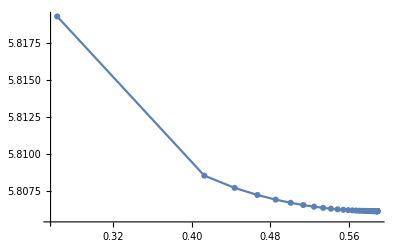

```mathematica
min=findMinimum[1,50];
Print[{min[[1]],min[[2]]}]
data=min[[3]];
ListPlot[data,Joined->True,PlotMarkers->Automatic,PlotRange->All]
```

```mathematica
Eigenvalues[Hb[J,P,Isospin,Λ,γMax,0.59,m1,m2,m3,project]]
```

{9.86135,9.78881,9.7598,9.73409,9.71284,9.69876,9.67824,9.64488,9.64251,9.62776,9.61561,9.59181,9.58808,9.57912,9.53697,9.52833,9.49039,9.47309,9.46735,9.44776,9.27989,9.25352,9.25128,9.21979,9.20611,9.19285,9.17237,9.13806,9.12831,9.12078,8.42156,8.34063,8.31711,8.27732,8.25622,8.24506,8.22595,8.1738,8.16564,8.15244,8.12626,8.11746,8.10115,8.08862,8.049,8.03713,8.01373,8.00223,7.99859,7.98158,7.41642,7.33379,7.32306,7.28654,7.28303,7.25877,7.24784,7.1934,7.1824,7.14872,7.12735,6.99437,6.69422,6.61054,6.58188,6.56297,6.46563,6.33868,5.94383,5.80611}